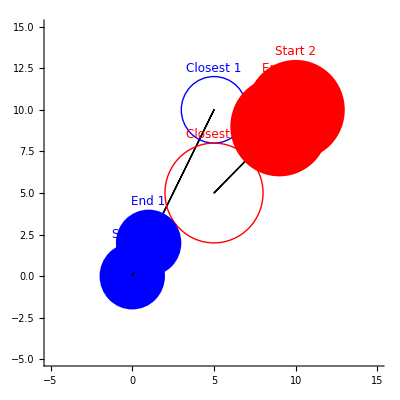

```mathematica
(*Function to solve the quadratic equation*)solveQuadratic[a_,b_,c_]:=Module[{discriminant,t1,t2},discriminant=b^2-4*a*c;
If[discriminant<0,{None,None},(*No real solutions*)If[discriminant==0,t1=-b/(2*a);{t1,None},(*One solution*)t1=(-b+Sqrt[discriminant])/(2*a);
t2=(-b-Sqrt[discriminant])/(2*a);

{t1,t2} (*Two solutions*)
]
]
];

(*Function to find the closest approach time*)
closestApproachTime[P1_,V1_,P2_,V2_,r1_,r2_]:=Module[{Rx,Ry,VrelX,VrelY,a,b,c,t1,t2},(*Relative position and velocity*)Rx=P2[[1]]-P1[[1]];
Ry=P2[[2]]-P1[[2]];
VrelX=V2[[1]]-V1[[1]];
VrelY=V2[[2]]-V1[[2]];
(*Coefficients of the quadratic equation*)a=VrelX^2+VrelY^2;
b=2*(Rx*VrelX+Ry*VrelY);
c=Rx^2+Ry^2-(r1+r2)^2;
(*Solve the quadratic equation*){t1,t2}=solveQuadratic[a,b,c];
{t1,t2}];

(*Function to get the positions of the circles at time t*)
circlePosition[P_,V_,t_]:=P+V*t

(*Example usage*)
P1={0,0};  (*Initial position of first circle*)
V1={1,2};  (*Velocity of first circle*)
P2={10,10};  (*Initial position of second circle*)
V2={-1,-1};  (*Velocity of second circle*)
r1=2;  (*Radius of first circle*)
r2=3;  (*Radius of second circle*)

{t1,t2}=closestApproachTime[P1,V1,P2,V2,r1,r2];

(*If t1 is not None,choose the valid time closest to 0*)
tClosest=If[t1>0,t1,t2];

(*Positions at start,closest approach,and end*)
pos1Start=P1;
pos2Start=P2;
pos1Closest=circlePosition[P1,V1,tClosest];
pos2Closest=circlePosition[P2,V2,tClosest];
pos1End=circlePosition[P1,V1,1];
pos2End=circlePosition[P2,V2,1];

(*Plot the positions*)
Graphics[{(*Start positions*)Blue,Disk[pos1Start,r1],Red,Disk[pos2Start,r2],(*Lines connecting centers*)Black,Line[{pos1Start,pos1Closest,pos1End}],Black,Line[{pos2Start,pos2Closest,pos2End}],(*Closest approach positions,without fill*)Blue,Style[Circle[pos1Closest,r1],Dashing[{}]],Red,Style[Circle[pos2Closest,r2],Dashing[{}]],(*End positions*)Blue,Disk[pos1End,r1],Red,Disk[pos2End,r2]},PlotRange->{{-5,15},{-5,15}},Axes->True,AspectRatio->1,Epilog->{Text[Style["Start 1",12,Blue],pos1Start+{0,r1+0.5}],Text[Style["Start 2",12,Red],pos2Start+{0,r2+0.5}],Text[Style["Closest 1",12,Blue],pos1Closest+{0,r1+0.5}],Text[Style["Closest 2",12,Red],pos2Closest+{0,r2+0.5}],Text[Style["End 1",12,Blue],pos1End+{0,r1+0.5}],Text[Style["End 2",12,Red],pos2End+{0,r2+0.5}]}]
```